```mathematica
(* CONSTANTS *)
α = 2.1683; 
a1 = -0.04531;
a2 = -1.0808;
mylist = Range[50] - 1;

(* GSEH Solution *)
```

```mathematica
vl[l_] = (l + 0.5) * Pi ;
```

```mathematica
vls = Map[vl, mylist]
vlsLength = Length[vls];
```

{1.5708,4.71239,7.85398,10.9956,14.1372,17.2788,20.4204,23.5619,26.7035,29.8451,32.9867,36.1283,39.2699,42.4115,45.5531,48.6947,51.8363,54.9779,58.1195,61.2611,64.4026,67.5442,70.6858,73.8274,76.969,80.1106,83.2522,86.3938,89.5354,92.677,95.8186,98.9602,102.102,105.243,108.385,111.527,114.668,117.81,120.951,124.093,127.235,130.376,133.518,136.659,139.801,142.942,146.084,149.226,152.367,155.509}

```mathematica
muns = NSolve[{-BesselJ[1, mu * 6.0] * (BesselY[1, mu * 4.0]/BesselJ[1, mu * 4.0] ) + BesselY[1, mu * 6.0] == 0, 0 <= mu <= 12* Pi}, mu];
munsLength = Length[muns]
```

23

```mathematica
muns = mu/.muns
```

{1.58047,3.14653,4.71569,6.28567,7.85597,9.42643,10.997,12.5676,14.1383,15.709,17.2797,18.8504,20.4211,21.9919,23.5626,25.1334,26.7041,28.2749,29.8457,31.4164,32.9872,34.558,36.1287}

```mathematica
CNFUNC[munN_] =-BesselY[1, munN * 4.0] / BesselJ[1, munN * 4.0];
```

```mathematica
CNS = Map[CNFUNC, muns];
```

```mathematica
λsquare[lVal_,muVal_] :=lVal^2 + muVal^2
```

```mathematica
λsquared = Transpose[Outer[λsquare, vls, muns]];
```

```mathematica
λsquared[[1,2]]
```

```mathematica
eu[n_,x_] := (1 / muns[[n]])* (
	a1 * x^2 * (
	CNS[[n]] * BesselJ[2, muns[[n]] * x]
	+ BesselY[2, muns[[n]] * x] 
)+
	a2 * (
	CNS[[n]] * BesselJ[0, muns[[n]] * x]
	+ BesselY[0, muns[[n]] * x]
)
)
```

```mathematica
ed[n_, x_] := -0.5 * x^2 * BesselY[0, muns[[n]] * x] * BesselY[2, muns[[n]] * x] - 0.5 * CNS[[n]]^2 * x^2 * BesselJ[0, muns[[n]] * x] * BesselJ[2, muns[[n]] * x]+ CNS[[n]] * (
0.5 * x^2 * (
BesselJ[0, muns[[n]] * x] - BesselJ[2, muns[[n]] * x]
) * BesselY[0, muns[[n]] * x]
- (1 / muns[[n]]) * x * BesselJ[0, muns[[n]] * x] * BesselY[1, muns[[n]] * x]
)
au[n_]:=eu[n, 6.0] - eu[n, 4.0] 
ad[n_]:=ed[n, 6.0] - ed[n, 4.0]
innerIterate[x_,z_,l_,n_]:=(
((-1)^(l-1) * 2 * au[n])
/
(vls[[l]]*ad[n] * (α^2 -λsquared[[n,l]] ))
)*(CNS[[n]] * BesselJ[1, muns[[n]] * x]+BesselY[1, muns[[n]] *x])*Cos[vls[[l]]*z]
```

```mathematica
psi[x_,z_]:=x *Sum[
innerIterate[x,z,lV,nV], {lV, 1, vlsLength}, {nV, 1, munsLength}
]
```

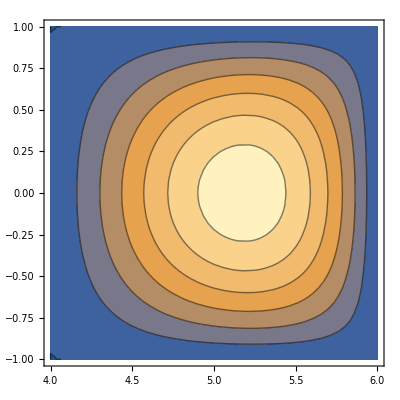

```mathematica
(* Grad-Shafranov Helmholtz Equation*)
ContourPlot[Evaluate[psi[x,z]], {x, 4.0, 6.0}, {z, -1.0, 1.0}]
```

```mathematica
psi[x,z];
```

```mathematica
(* Grad-Shafranov Helmholtz Equation*)
(* NOTE: I've made the substitutions for a1 and a2 here to simplify to two equations. *)

(*eq1 = x * D[ (1/x)* D[psi[x,z]], x] + D[psi[x,z], {z,2}] == -x * jϕ ;*)


eq2 = x *( D[ (1/x)* D[psi[x,z],x], x]) + D[psi[x,z], {z,2}] - (a1 * x^2 - a2 - α^2 * psi[x,z]) 
eqsub2 = x D[(1/x) D[spsi[x,z],x],x] + D[spsi[x,z], {z,2}] - (sa1 * x^2 - sa2 - sα^2 * spsi[x,z]) 
(* DSolve[eq2, psi[x,z], {x, z}] *)



(* How do we representing jϕ here? What are B0 and μ0? (in the sense do we know what value we can give them)*)
```

sa2-sa1 x^2+sα^2 spsi[x,z]+spsi^(0,2)[x,z]+x (-(spsi^(1,0)[x,z])/x^2+(spsi^(2,0)[x,z])/x)

```mathematica
subs = {spsi[x,z]-> psi[x,z]};
```

```mathematica
eqsub2 /. subs;
```

```mathematica
eq2 /. {x-> 5, z-> 0}
```

0.00170741

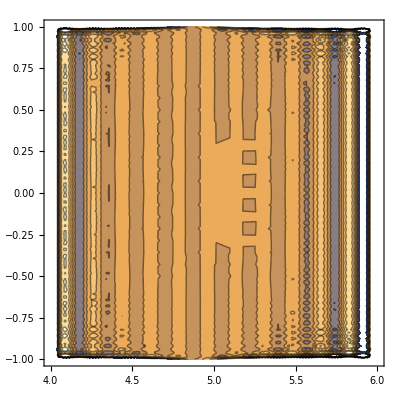

```mathematica
ContourPlot[Evaluate[eq2, {x, 4.0, 6.0}, {z, -1.0, 1.0}]]
```

```mathematica
(* Checking eq 5c-5d, part solution to expansion of eq 4a-4c *)
em1 = D[R[x], {x, 2}] + (1/x) D[R[x], x] + (v^2 - (1/x)^2)R[x] == 0
bc1 = R[4] == 0
bc2 = R[6] == 0
```

(v^2-1/x^2) R[x]+R'[x]/x+R''[x]==0

R[4]==0

R[6]==0

```mathematica
DSolve[{em1, bc1, bc2}, R,x]
```

```mathematica
current[x_] = (-1/x) * (a1*x^2-a2-α^2 * psi[x,0]);
```

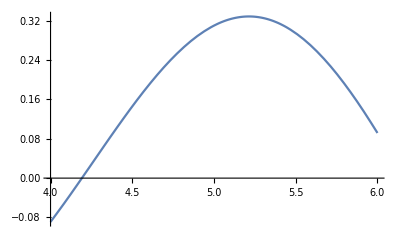

```mathematica
Plot[current[x], {x, 4.0, 6.0}]
```

```mathematica
maxCurrent =Maximize[{Abs[current[x]],4.0<=x<=6.0},x]
```

{0.258873,{x→4.}}

```mathematica
maxCurrentT = FindMaximum[{Abs[current[x]], 4.0<=x<=6.0}, x ]
```

{0.258872,{x→4.}}

```mathematica
normalisedCurrent[x_] = current[x] / maxCurrent;
```

```mathematica
Plot[normalisedCurrent[x], {x, 4.0, 6.0}]
```